# 微分方程式

人口

増加率は現在の人口に比例

```mathematica
e={y'[t]==a y[t]}
```

{y'[t]==a y[t]}

```mathematica
DSolve[e,y[t],t]
```

{{y[t]→ⅇ^(a t) C[1]}}

人口には最大値がありこれによって各時点の増加率が決まる(ヴエアファルスト)
dy / dt == k y(m-y / m)
mが最大値

```mathematica
e2={y'[t]==k y[t](m-y[t])/m,y[0]==y0}
```

{y'[t]==(k (m-y[t]) y[t])/m,y[0]==y0}

```mathematica
sol2=DSolve[e2,y[t],t]
```

Solve::ifun: 逆関数がSolveで使われているため，求められない解がある可能性があります．解の詳細情報にはReduceをお使いください．

{{y[t]→(ⅇ^(k t) m y0)/(m-y0+ⅇ^(k t) y0)}}

```mathematica
f2=y[t]/.sol2/.{C[1]->0,k->1,m->200000,y0->100}
```

{(20000000 ⅇ^t)/(199900+100 ⅇ^t)}

```mathematica
Table[f2,{t,0.1,10,0.1}]//N
```

{{11.0517},{12.2139},{13.4984},{14.9179},{16.4867},{18.2204},{20.1365},{22.254},{24.5942},{27.1805},{30.0387},{33.1973},{36.6881},{40.5458},{44.8091},{49.5205},{54.7272},{60.4812},{66.8399},{73.867},{81.6324},{90.2139},{99.6971},{110.177},{121.757},{134.554},{148.694},{164.32},{181.586},{200.664},{221.744},{245.037},{270.773},{299.208},{330.624},{365.332},{403.677},{446.037},{492.832},{544.522},{601.618},{664.68},{734.329},{811.245},{896.183},{989.968},{1093.51},{1207.83},{1334.01},{1473.27},{1626.96},{1796.53},{1983.6},{2189.93},{2417.46},{2668.32},{2944.82},{3249.49},{3585.12},{3954.71},{4361.56},{4809.24},{5301.63},{5842.92},{6437.64},{7090.69},{7807.31},{8593.14},{9454.16},{10396.8},{11427.7},{12554.2},{13783.5},{15123.5},{16582.2},{18167.7},{19888.4},{21752.6},{23768.5},{25944.},{28286.6},{30803.4},{33500.3},{36382.7},{39454.2},{42717.4},{46172.9},{49819.3},{53653.2},{57668.9},{61858.1},{66210.1},{70711.5},{75346.6},{80097.3},{84943.5},{89863.1},{94832.7},{99828.1},{104824.}}

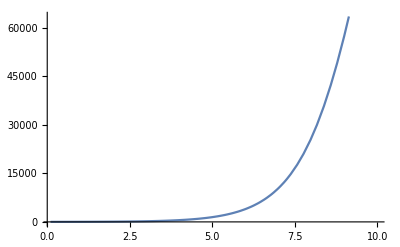

```mathematica
Plot[f2,{t,0.1,10}]
```

ヴエアファルストmodelは、ただし、初期値を仮定しないとこれが無限大となる。

```mathematica
e2={y'[t]==k y[t](m-y[t])/m}
```

{y'[t]==(k (m-y[t]) y[t])/m}

```mathematica
sol2=DSolve[e2,y[t],t]
```

{{y[t]→(ⅇ^(k t+m C[1]) m)/(-1+ⅇ^(k t+m C[1]))}}

```mathematica
f2=y[t]/.sol2/.{C[1]->0,k->1,m->200000,t->0}
```

Power::infy: 無限式1/0が見付かりました．

{ComplexInfinity}

```mathematica
f2=y[t]/.sol2/.{C[1]->0,k->1,m->200000}
```

{(200000 ⅇ^t)/(-1+ⅇ^t)}

```mathematica
Table[f2,{t,0.1,10,0.1}]//N
```

{{2.10167×10^6},{1.10333×10^6},{771659.},{606649.},{508299.},{443274.},{397287.},{363193.},{337024.},{316395.},{299792.},{286203.},{274926.},{265462.},{257443.},{250594.},{244703.},{239607.},{235175.},{231304.},{227909.},{224922.},{222286.},{219954.},{217885.},{216047.},{214410.},{212949.},{211645.},{210479.},{209435.},{208499.},{207659.},{206905.},{206228.},{205618.},{205070.},{204577.},{204132.},{203731.},{203370.},{203045.},{202751.},{202486.},{202247.},{202031.},{201836.},{201660.},{201500.},{201357.},{201227.},{201109.},{201003.},{200907.},{200821.},{200742.},{200671.},{200607.},{200549.},{200497.},{200450.},{200407.},{200368.},{200333.},{200301.},{200272.},{200246.},{200223.},{200202.},{200183.},{200165.},{200149.},{200135.},{200122.},{200111.},{200100.},{200091.},{200082.},{200074.},{200067.},{200061.},{200055.},{200050.},{200045.},{200041.},{200037.},{200033.},{200030.},{200027.},{200025.},{200022.},{200020.},{200018.},{200017.},{200015.},{200014.},{200012.},{200011.},{200010.},{200009.}}